```mathematica
gravity=10;
withDrag[p0_,v0_,drag_]:=Module[{p},p[t_]:=Evaluate@Array[Unique[][t]&,3];
p[t]/.NDSolve[{p[0]==p0,p'[0]==v0,p''[t]==drag*Norm[p'[t]]*p'[t]+{0,0,-gravity}},p[t],{t,0,5}]//First]

track[t_]=withDrag[{0,0,0},{0,10^2,10},0.001];
ParametricPlot3D[track[t],{t,0,5},BoxRatios->1]
```

-Graphics3D-

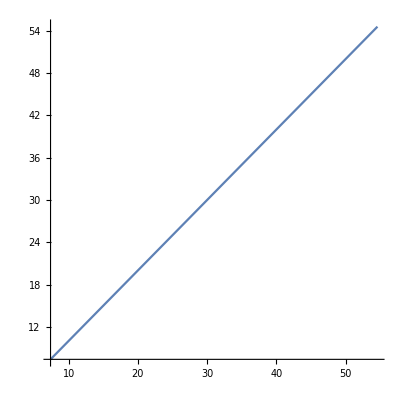

```mathematica
Clear[f,g,x,y,a,b,t,gamma,track];
f[{x_,y_}]:=x^2+y^2;
g[{x_,y_}]:=Grad[f[{a,b}],{a,b}]/.{a->x,b->y};
gamma[{x_,y_}]:=Module[{p},p[t_]:=Evaluate@Array[Unique[][t]&,2];
p[t]/.DSolve[{p[0]=={x,y},p'[t]==g[p[t]]},p[t],t]];

ParametricPlot[gamma[{1,1}]/.t->u,{u,1,2}]
```